NOTE (2026-11-10): the inputs of this notebook were corrected against ENSDF: Fr-223 alpha branch 6e-3 -> 6e-5 (0.006 %); At-219 branches b8a/b8b swapped back (alpha 0.936 to Bi-215, beta 0.064 to Rn-219); Po-215 beta branch 2.3e-4 -> 2.3e-6; decay constants of the two Po-215 daughters (n12/n13: Pb-211 and At-215) and of the two Bi-211 daughters (n15/n16: Tl-207 and Po-211) were assigned to the wrong nodes and are swapped, so At-215 is now n13 and Po-211 is n16. The plot and result cells at the end now use n13 and n16. The saved outputs, equations and plots below were produced with the OLD inputs and are stale until the notebook is re-evaluated. The original, uncorrected notebook is in villano-lab/L3He_paper2023, neutron-bknd-spectra/decay_chains/.

```mathematica
λ1:= 1; 
λ2:=242*^9;
λ3:=215*^2; 
λ4:=323*^5; 
λ5:=137*^8; 
λ6:= 168*^11; 
λ7:=225*^8;
λ8:= 396*^12; 
λ9:=560*^13;
λ10:= 487*^11; 
λ11:=125*^17; 
λ12 := 102*^11;
λ13 := 222*^18;
λ14 := 173*^12;
λ15 := 775*^11;
λ16 :=430*^14;
b4b:=9862*^-4;
b4a:=138*^-4; 
b6b:= 9999*^-4;
b6a:= 6*^-5;
b8b :=64*^-3; 
b8a:=936*^-3;b11b:=1*^0;b11a:=23*^-7;b14b:=9972*^-4;b14a:=28*^-4;
```

```mathematica
m[l1_,l2_,l3_,l4_,l5_,l6_,l7_,l8_,l9_,l10_,l11_,l12_,l13_,l14_,l15_,l16_,b4a_,b4b_,b6a_,b6b_,b8a_,b8b_,b11a_,b11b_,b14a_,b14b_]:= -{{l1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{-l1,l2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-l2,l3,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,-l3,l4,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-l4*b4b, l5, 0,0,0,0,0,0,0,0,0,0,0,0}, {0,0,0,-l4*b4a,0, l6,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,-l5,-l6*b6b, l7,0,0,0,0,0,0,0,0,0,0},{0, 0, 0, 0, 0, -l6*b6a, 0, l8,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,-l7,-l8*b8b, l9, 0, 0, 0, 0, 0, 0, 0,0}, {0,0,0,0,0,0,0,-l8*b8a,0, l10,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,-l9,-l10,l11,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-l11*b11b,l12,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-l11*b11a,0,l13,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-l12,-l13,l14,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-l14*b14b,l15,0,0} ,{0,0,0,0,0,0,0,0,0,0,0,0,0,-l14*b14a,0,l16,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,-l15,-l16,0}}
```

```mathematica
f := {n1[t],n2[t],n3[t],n4[t],n5[t],n6[t],n7[t],n8[t],n9[t],n10[t],n11[t],n12[t],n13[t],n14[t],n15[t],n16[t],n17[t]}
```

```mathematica
LHS = m[λ1,λ2,λ3,λ4,λ5,λ6,λ7,λ8,λ9,λ10,λ11,λ12,λ13,λ14,λ15,λ16,b4a,b4b,b6a,b6b,b8a,b8b,b11a,b11b,b14a,b14b].f
```

{-n1[t],n1[t]-242000000000 n2[t],242000000000 n2[t]-21500 n3[t],21500 n3[t]-32300000 n4[t],31854260 n4[t]-13700000000 n5[t],445740 n4[t]-16800000000000 n6[t],13700000000 n5[t]+16798320000000 n6[t]-22500000000 n7[t],1008000000 n6[t]-396000000000000 n8[t],22500000000 n7[t]+25344000000000 n8[t]-5600000000000000 n9[t],-48700000000000 n10[t]+370656000000000 n8[t],48700000000000 n10[t]-12500000000000000000 n11[t]+5600000000000000 n9[t],12500000000000000000 n11[t]-10200000000000 n12[t],28750000000000 n11[t]-222000000000000000000 n13[t],10200000000000 n12[t]+222000000000000000000 n13[t]-173000000000000 n14[t],172515600000000 n14[t]-77500000000000 n15[t],484400000000 n14[t]-43000000000000000 n16[t],77500000000000 n15[t]+43000000000000000 n16[t]}

```mathematica
Eqns1 = LHS[[1]]==n1'[t]
```

-n1[t]==n1'[t]

```mathematica
Eqns2 = LHS[[2]]==n2'[t]
```

n1[t]-242000000000 n2[t]==n2'[t]

```mathematica
Eqns3 = LHS[[3]]==n3'[t]
```

242000000000 n2[t]-21500 n3[t]==n3'[t]

```mathematica
Eqns4 = LHS[[4]]==n4'[t]
```

21500 n3[t]-32300000 n4[t]==n4'[t]

```mathematica
Eqns5 = LHS[[5]]==n5'[t]
```

31854260 n4[t]-13700000000 n5[t]==n5'[t]

```mathematica
Eqns6 = LHS[[6]]==n6'[t]
```

445740 n4[t]-16800000000000 n6[t]==n6'[t]

```mathematica
Eqns7 = LHS[[7]]==n7'[t]
```

13700000000 n5[t]+16798320000000 n6[t]-22500000000 n7[t]==n7'[t]

```mathematica
Eqns8 = LHS[[8]]==n8'[t]
```

1008000000 n6[t]-396000000000000 n8[t]==n8'[t]

```mathematica
Eqns9 = LHS[[9]]==n9'[t]
```

22500000000 n7[t]+25344000000000 n8[t]-5600000000000000 n9[t]==n9'[t]

```mathematica
Eqns10 = LHS[[10]]==n10'[t]
```

-48700000000000 n10[t]+370656000000000 n8[t]==n10'[t]

```mathematica
Eqns11 = LHS[[11]]==n11'[t]
```

48700000000000 n10[t]-12500000000000000000 n11[t]+5600000000000000 n9[t]==n11'[t]

```mathematica
Eqns12 = LHS[[12]]==n12'[t]
```

12500000000000000000 n11[t]-10200000000000 n12[t]==n12'[t]

```mathematica
Eqns13 = LHS[[13]]==n13'[t]
```

28750000000000 n11[t]-222000000000000000000 n13[t]==n13'[t]

```mathematica
Eqns14 = LHS[[14]]==n14'[t]
```

10200000000000 n12[t]+222000000000000000000 n13[t]-173000000000000 n14[t]==n14'[t]

```mathematica
Eqns15 = LHS[[15]]==n15'[t]
```

172515600000000 n14[t]-77500000000000 n15[t]==n15'[t]

```mathematica
Eqns16 = LHS[[16]]==n16'[t]
```

484400000000 n14[t]-43000000000000000 n16[t]==n16'[t]

```mathematica
Eqns17 = LHS[[17]]==n17'[t]
```

77500000000000 n15[t]+43000000000000000 n16[t]==n17'[t]

```mathematica
sol=NDSolve[{Eqns1,Eqns2,Eqns3,Eqns4,Eqns5,Eqns6,Eqns7,Eqns8,Eqns9,Eqns10,Eqns11,Eqns12,Eqns13,Eqns14,Eqns15,Eqns16,Eqns17,n1[0]==1,n2[0]==0,n3[0]==0,n4[0]==0,n5[0]==0,n6[0]==0,n7[0]==0,n8[0]==0,n9[0]==0,n10[0]==0,n11[0]==0,n12[0]==0,n13[0]==0,n14[0]==0,n15[0]==0,n16[0]==0,n17[0]==0},{n1,n2,n3,n4,n5,n6,n7,n8,n9,n10,n11,n12,n13,n14,n15,n16,n17},{t,0,1}];
```

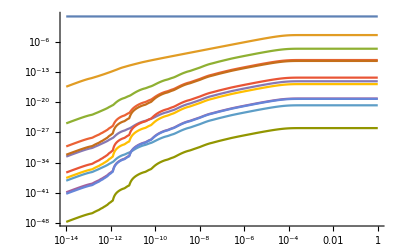

```mathematica
LogLogPlot[Evaluate[{n1[t]/n1[t],n3[t]/n1[t],n4[t]/n1[t],n5[t]/n1[t],n6[t]/n1[t],n7[t]/n1[t],n8[t]/n1[t],n9[t]/n1[t],n11[t]/n1[t],n13[t]/n1[t],n14[t]/n1[t],n16[t]/n1[t]}/. sol],{t,1*^-14,1},PlotRange->All]
```

```mathematica
Evaluate[64836*^-21*{n1[1]/n1[1],n3[1]/n1[1],n4[1]/n1[1],n5[1]/n1[1],n6[1]/n1[1],n7[1]/n1[1],n8[1]/n1[1],n9[1]/n1[1],n11[1]/n1[1],n13[1]/n1[1],n14[1]/n1[1],n16[1]/n1[1]}/. sol]
```

{{16209/250000000000000000000,3.01577×10^-21,2.0074×10^-24,4.66746×10^-27,5.32606×10^-32,2.88173×10^-27,1.35572×10^-37,1.15784×10^-32,5.18712×10^-36,6.71755×10^-43,3.74793×10^-31,4.22208×10^-36}}